```mathematica
Table[ChromEmbedGraphInPlantri8[allGraphs5,k]
```

```mathematica
Table[{allGraphs5[k,"embed"],k},{k,allGraphs5AtomKeys}]//Sort
```

{{0,29524},{0,29608},{3,31714},{3,36166},{4,31984},{4,36194},{5,36898},{5,51478},{6,29527},{6,29605},{7,38281},{8,30334},{8,31738},{8,31954},{8,36086},{8,36112},{8,49210},{9,31711},{9,36085},{9,38308},{10,29525},{10,29633},{10,29767},{10,29797},{11,29551},{11,29888},{11,30253},{11,30586},{11,49207},{11,49220},{12,32684},{12,56012},{13,36817},{13,51475},{14,29537},{14,29768},{14,29857},{16,30496},{16,39014},{16,49208},{16,58288},{16,59048},{18,52232},{18,56770},{20,29533},{20,32441},{20,56011},{21,49963},{26,49972},{29,30262},{29,49216},{31,29560}}

```mathematica
allGraphs5[29608,"graph"]
```

-Graphics-

```mathematica
gamma1Key
```

29608

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,gamma1Key],x]]
```

{0,0,0,0,0,1586,33088,146892,231967,163709,57997,10874,1080,53,1}

```mathematica
femb=FindFullFormula[EmbedGraphInPlantri8[allGraphs5,gamma1Key]];
```

```mathematica
Length[femb]
```

647247

```mathematica
Select[femb,SymbolLevel[#]==4&]//Length
```

0

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,alfa1Key],x]]
```

{0,0,0,0,3,1657,33021,145463,229683,162452,57705,10845,1079,53,1}

```mathematica
Select[femb,SymbolLevel[#]==5&]//Length
```

1586

```mathematica
femb2=FindFullFormula[EmbedGraphInPlantri8[allGraphs5,alfa1Key]];
```

```mathematica
allGraphs5[alfa1Key,"colofour"]
```

v13x24x5

```mathematica
Select[femb2,SymbolLevel[#]==4&]
```

{v1adx259bx3cgx468h,v1acx259hx3bdx468g,v19cx25ahx3bdx468g}

```mathematica
Graph[EmbedGraphInPlantri8[allGraphs5,gamma1Key],GraphLayout->"CircularEmbedding"]//PlanarGraphQ
```

False

```mathematica
IsCoreShape[set_,nodes_]:=(Length[set]==nodes-1&&(MemberQ[set,{1,3}]||MemberQ[set,{1,4}]||MemberQ[set,{2,4}]||MemberQ[set,{2,5}]||MemberQ[set,{3,5}])) ||(Length[set]==nodes-2&&(
(MemberQ[set,{1,3}]&&MemberQ[set,{2,5}])
||(MemberQ[set,{1,3}]&&MemberQ[set,{2,4}])
||(MemberQ[set,{1,4}]&&MemberQ[set,{2,5}])
||(MemberQ[set,{1,4}]&&MemberQ[set,{3,5}])
||(MemberQ[set,{2,4}]&&MemberQ[set,{3,5}])

))
```

```mathematica
MyFormatSymbol[sym_,goodValue_]:=With[{s=SymbolToSets[sym]
},
With[{nodes=Length[Flatten[s]]},
If[IsCoreShape[s,nodes],
Framed[ColorShape2[ s],Background->Yellow],
If[MemberQ[goodValue,s],
Framed[ColorShape2[ s],Background->LightYellow],
ColorShape2[ s]
],ColorShape2[ s]]
]
]
```

```mathematica
ColorShape2[sets_]:=Style[SetsToLabel[sets],If[HasQuadrilateralPattern[sets],Darker[Green],If[HasTrianglePattern[sets],Red,Black]]]
```

```mathematica
WriteFormula[sets_]:=Map[MyFormatSymbol[#,7]&,Select[FindFullFormula[GraphFromPatterns[sets]],SymbolLevel[#]==4&]]
```

```mathematica
FindFullFormula4[g_]:=Block[{},
Monitor[
formulaDepth=0;FindFullFormula4[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFullFormula4[g_,v_]:=Block[{edge,pos1,pos2,v2,result={},result1,result2,clique},
If[CompleteGraphQ[g],
result=Select[{SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]},SymbolLevel[#]==4&]
,
clique=First[FindClique[g]];
If[Length[clique]<=4,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula4[EdgeAdd[g,edge],v],
FindFullFormula4[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
,
{}
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
EmbedGraphInPlantri8b[key_]:=Block[{val=allGraphs5[key], sets, reference={1,2,3,4,5}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ plantri8,14];
g=EdgeDelete[ g,{1<->2,2<->3,3<->4,4<->5,5<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

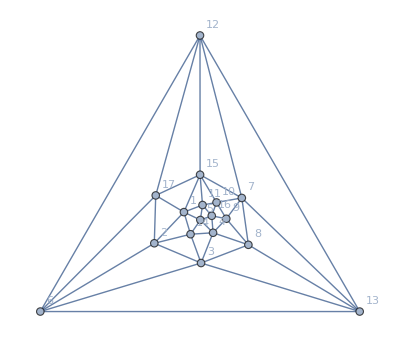

```mathematica
plantri8
```

```mathematica
EmbedGraphInPlantri8b[alfa1Key]
```

```mathematica
EnrichSymbol[symbol_,sets_]:=Block[{result=SymbolToSets[symbol]},
Table[
result=Table[
If[Intersection[r,s]≠{},Sort[DeleteDuplicates[Union[r,s]]],r]
,{r,result}]
,
{s,sets}
];
SetsToSymbol2[result,StringTake[SymbolName[symbol],1]]
]
```

```mathematica
EnrichSymbol[v1acx27bx59dhx68fg,allGraphs5[36166,"vertexsets"]]
```

v13acx247bx59dhx68fg

```mathematica
TableForm[Table[
ShowGraph5Least[k]->Framed[Multicolumn[With[{g=EmbedGraphInPlantri8b[k]},
Map[MyFormatSymbol[EnrichSymbol[#,allGraphs5[k,"vertexsets"]],VertexCount[g]]&, Sort[FindFullFormula4[g],CompareSymbols]]
]]],{k,Join[alfa1s,quads,{lambdaKey}]}],TableDepth->1]
```

-Graphics-361660→13ac♁247b♁59dh♁68fg | 139c♁247b♁5adh♁68fg
137g♁24ac♁568f♁9bdh | 
-Graphics-317380→14ac♁259df♁37bh♁68g | 14ad♁259c♁37bh♁68fg | 1467♁258ac♁3fg♁9bdh
14ac♁259df♁37gh♁68b | 146a♁259df♁37bh♁8cg | 1467♁258ac♁39bh♁dfg
14ac♁259d♁37bh♁68fg | 146a♁259df♁37gh♁8bc | 
-Graphics-296080→
-Graphics-361120→13ac♁259df♁467b♁8gh | 13cg♁259df♁467b♁8ah | 137g♁258ac♁46f♁9bdh
13ac♁259df♁47bh♁68g | 13cg♁259df♁47bh♁68a | 139c♁25ad♁47bh♁68fg
13ac♁259d♁47bh♁68fg | 137g♁258ac♁4bdh♁69f | 
-Graphics-317140→14ac♁29bd♁357h♁68fg | 1467♁28fg♁35ac♁9bdh
14ad♁29bc♁357h♁68fg | 
-Graphics-360850→13ac♁28fg♁467b♁59dh | 137g♁28ac♁4bdh♁569f | 139c♁2dfg♁467b♁58ah
13cg♁29df♁467b♁58ah | 137g♁28bc♁4adh♁569f | 139c♁2dfg♁47bh♁568a
13cg♁29df♁47bh♁568a | 137g♁29bc♁4adh♁568f | 139c♁28fg♁467b♁5adh
-Graphics-296050→167g♁24df♁39bc♁58ah | 168a♁24bc♁37gh♁59df | 18ac♁24bd♁37gh♁569f
167g♁24df♁39bh♁58ac | 168g♁24ac♁37bh♁59df | 18cg♁24ad♁37bh♁569f
-Graphics-295270→167g♁28ac♁359f♁4bdh | 168a♁2dfg♁359c♁47bh | 18ac♁2dfg♁359h♁467b
167g♁28bc♁359f♁4adh | 168g♁29df♁35ac♁47bh | 18cg♁29df♁35ah♁467b
-Graphics-317110→14ac♁29bd♁37gh♁568f | 14ad♁29bc♁37gh♁568f | 1467♁2dfg♁39bc♁58ah
14ad♁28bc♁37gh♁569f | 146a♁28bc♁37gh♁59df | 1467♁2dfg♁39bh♁58ac
14ad♁28cg♁37bh♁569f | 146a♁28cg♁37bh♁59df | 1467♁28fg♁39bc♁5adh
-Graphics-295510→167g♁258ac♁39bh♁4df | 168a♁259df♁3cg♁47bh | 168g♁259df♁37bh♁4ac | 18cg♁259df♁3ah♁467b
167g♁258ac♁39f♁4bdh | 168a♁259df♁37gh♁4bc | 18ac♁259df♁3gh♁467b | 18cg♁259df♁37bh♁46a
167g♁258f♁39bc♁4adh | 168g♁259df♁3ac♁47bh | 18ac♁259df♁37gh♁46b | 
-Graphics-206653→13ac♁247b♁59dh♁68fg | 13cg♁29df♁47bh♁568a | 139c♁2dfg♁47bh♁568a | 14ac♁29bd♁37gh♁568f | 146a♁28bc♁37gh♁59df | 167g♁24df♁39bc♁58ah | 168a♁24bc♁37gh♁59df | 18ac♁24bd♁37gh♁569f
13ac♁259df♁467b♁8gh | 137g♁24ac♁568f♁9bdh | 139c♁247b♁5adh♁68fg | 14ad♁259c♁37bh♁68fg | 146a♁28cg♁37bh♁59df | 167g♁24df♁39bh♁58ac | 168a♁259df♁3cg♁47bh | 18ac♁259df♁3gh♁467b
13ac♁259df♁47bh♁68g | 137g♁258ac♁4bdh♁69f | 139c♁25ad♁47bh♁68fg | 14ad♁28bc♁37gh♁569f | 1467♁2dfg♁39bc♁58ah | 167g♁258ac♁39bh♁4df | 168a♁259df♁37gh♁4bc | 18ac♁259df♁37gh♁46b
13ac♁259d♁47bh♁68fg | 137g♁258ac♁46f♁9bdh | 139c♁28fg♁467b♁5adh | 14ad♁28cg♁37bh♁569f | 1467♁2dfg♁39bh♁58ac | 167g♁258ac♁39f♁4bdh | 168g♁24ac♁37bh♁59df | 18cg♁24ad♁37bh♁569f
13ac♁28fg♁467b♁59dh | 137g♁28ac♁4bdh♁569f | 14ac♁259df♁37bh♁68g | 14ad♁29bc♁357h♁68fg | 1467♁258ac♁3fg♁9bdh | 167g♁258f♁39bc♁4adh | 168g♁259df♁3ac♁47bh | 18cg♁259df♁3ah♁467b
13cg♁259df♁467b♁8ah | 137g♁28bc♁4adh♁569f | 14ac♁259df♁37gh♁68b | 14ad♁29bc♁37gh♁568f | 1467♁258ac♁39bh♁dfg | 167g♁28ac♁359f♁4bdh | 168g♁259df♁37bh♁4ac | 18cg♁259df♁37bh♁46a
13cg♁259df♁47bh♁68a | 137g♁29bc♁4adh♁568f | 14ac♁259d♁37bh♁68fg | 146a♁259df♁37bh♁8cg | 1467♁28fg♁35ac♁9bdh | 167g♁28bc♁359f♁4adh | 168g♁29df♁35ac♁47bh | 18cg♁29df♁35ah♁467b
13cg♁29df♁467b♁58ah | 139c♁2dfg♁467b♁58ah | 14ac♁29bd♁357h♁68fg | 146a♁259df♁37gh♁8bc | 1467♁28fg♁39bc♁5adh | 168a♁2dfg♁359c♁47bh | 18ac♁2dfg♁359h♁467b |

```mathematica
TableForm[Table[
ShowGraph5Least[k]->Framed[Multicolumn[With[{g=EmbedGraphInPlantri8b[k]},
Map[MyFormatSymbol[#,VertexCount[g]]&,Sort[FindFullFormula4[g],CompareSymbols] ]
]]],{k,Join[alfa1s,quads,{lambdaKey}]}],TableDepth->1]
```

-Graphics-361660→1ac♁27b♁59dh♁68fg | 19c♁27b♁5adh♁68fg
17g♁2ac♁568f♁9bdh | 
-Graphics-317380→1ac♁29df♁37bh♁68g | 1ad♁29c♁37bh♁68fg | 167♁28ac♁3fg♁9bdh
1ac♁29df♁37gh♁68b | 16a♁29df♁37bh♁8cg | 167♁28ac♁39bh♁dfg
1ac♁29d♁37bh♁68fg | 16a♁29df♁37gh♁8bc | 
-Graphics-296080→
-Graphics-361120→1ac♁29df♁467b♁8gh | 1cg♁29df♁467b♁8ah | 17g♁28ac♁46f♁9bdh
1ac♁29df♁47bh♁68g | 1cg♁29df♁47bh♁68a | 19c♁2ad♁47bh♁68fg
1ac♁29d♁47bh♁68fg | 17g♁28ac♁4bdh♁69f | 
-Graphics-317140→1ac♁29bd♁37h♁68fg | 167♁28fg♁3ac♁9bdh
1ad♁29bc♁37h♁68fg | 
-Graphics-360850→1ac♁28fg♁467b♁59dh | 17g♁28ac♁4bdh♁569f | 19c♁2dfg♁467b♁58ah
1cg♁29df♁467b♁58ah | 17g♁28bc♁4adh♁569f | 19c♁2dfg♁47bh♁568a
1cg♁29df♁47bh♁568a | 17g♁29bc♁4adh♁568f | 19c♁28fg♁467b♁5adh
-Graphics-296050→167g♁2df♁39bc♁58ah | 168a♁2bc♁37gh♁59df | 18ac♁2bd♁37gh♁569f
167g♁2df♁39bh♁58ac | 168g♁2ac♁37bh♁59df | 18cg♁2ad♁37bh♁569f
-Graphics-295270→167g♁28ac♁39f♁4bdh | 168a♁2dfg♁39c♁47bh | 18ac♁2dfg♁39h♁467b
167g♁28bc♁39f♁4adh | 168g♁29df♁3ac♁47bh | 18cg♁29df♁3ah♁467b
-Graphics-317110→1ac♁29bd♁37gh♁568f | 1ad♁29bc♁37gh♁568f | 167♁2dfg♁39bc♁58ah
1ad♁28bc♁37gh♁569f | 16a♁28bc♁37gh♁59df | 167♁2dfg♁39bh♁58ac
1ad♁28cg♁37bh♁569f | 16a♁28cg♁37bh♁59df | 167♁28fg♁39bc♁5adh
-Graphics-295510→167g♁28ac♁39bh♁4df | 168a♁29df♁3cg♁47bh | 168g♁29df♁37bh♁4ac | 18cg♁29df♁3ah♁467b
167g♁28ac♁39f♁4bdh | 168a♁29df♁37gh♁4bc | 18ac♁29df♁3gh♁467b | 18cg♁29df♁37bh♁46a
167g♁28f♁39bc♁4adh | 168g♁29df♁3ac♁47bh | 18ac♁29df♁37gh♁46b | 
-Graphics-206653→13ac♁247b♁59dh♁68fg | 13cg♁29df♁47bh♁568a | 139c♁2dfg♁47bh♁568a | 14ac♁29bd♁37gh♁568f | 146a♁28bc♁37gh♁59df | 167g♁24df♁39bc♁58ah | 168a♁24bc♁37gh♁59df | 18ac♁24bd♁37gh♁569f
13ac♁259df♁467b♁8gh | 137g♁24ac♁568f♁9bdh | 139c♁247b♁5adh♁68fg | 14ad♁259c♁37bh♁68fg | 146a♁28cg♁37bh♁59df | 167g♁24df♁39bh♁58ac | 168a♁259df♁3cg♁47bh | 18ac♁259df♁3gh♁467b
13ac♁259df♁47bh♁68g | 137g♁258ac♁4bdh♁69f | 139c♁25ad♁47bh♁68fg | 14ad♁28bc♁37gh♁569f | 1467♁2dfg♁39bc♁58ah | 167g♁258ac♁39bh♁4df | 168a♁259df♁37gh♁4bc | 18ac♁259df♁37gh♁46b
13ac♁259d♁47bh♁68fg | 137g♁258ac♁46f♁9bdh | 139c♁28fg♁467b♁5adh | 14ad♁28cg♁37bh♁569f | 1467♁2dfg♁39bh♁58ac | 167g♁258ac♁39f♁4bdh | 168g♁24ac♁37bh♁59df | 18cg♁24ad♁37bh♁569f
13ac♁28fg♁467b♁59dh | 137g♁28ac♁4bdh♁569f | 14ac♁259df♁37bh♁68g | 14ad♁29bc♁357h♁68fg | 1467♁258ac♁3fg♁9bdh | 167g♁258f♁39bc♁4adh | 168g♁259df♁3ac♁47bh | 18cg♁259df♁3ah♁467b
13cg♁259df♁467b♁8ah | 137g♁28bc♁4adh♁569f | 14ac♁259df♁37gh♁68b | 14ad♁29bc♁37gh♁568f | 1467♁258ac♁39bh♁dfg | 167g♁28ac♁359f♁4bdh | 168g♁259df♁37bh♁4ac | 18cg♁259df♁37bh♁46a
13cg♁259df♁47bh♁68a | 137g♁29bc♁4adh♁568f | 14ac♁259d♁37bh♁68fg | 146a♁259df♁37bh♁8cg | 1467♁28fg♁35ac♁9bdh | 167g♁28bc♁359f♁4adh | 168g♁29df♁35ac♁47bh | 18cg♁29df♁35ah♁467b
13cg♁29df♁467b♁58ah | 139c♁2dfg♁467b♁58ah | 14ac♁29bd♁357h♁68fg | 146a♁259df♁37gh♁8bc | 1467♁28fg♁39bc♁5adh | 168a♁2dfg♁359c♁47bh | 18ac♁2dfg♁359h♁467b |

```mathematica
TableForm[Table[
ShowGraph5Least[k]->Framed[Multicolumn[With[{g=EmbedGraphInPlantri8b[k]},
Sort[VertexList[g]]
]]],{k,Join[alfa1s,quads,{lambdaKey}]}],TableDepth->1]
```

-Graphics-361660→1 | 7 | 11 | 16
2 | 8 | 12 | 17
5 | 9 | 13 | 
6 | 10 | 15 | 
-Graphics-317380→1 | 7 | 11 | 16
2 | 8 | 12 | 17
3 | 9 | 13 | 
6 | 10 | 15 | 
-Graphics-296080→1 | 7 | 11 | 16
2 | 8 | 12 | 17
3 | 9 | 13 | 
6 | 10 | 15 | 
-Graphics-361120→1 | 7 | 11 | 16
2 | 8 | 12 | 17
4 | 9 | 13 | 
6 | 10 | 15 | 
-Graphics-317140→1 | 7 | 11 | 16
2 | 8 | 12 | 17
3 | 9 | 13 | 
6 | 10 | 15 | 
-Graphics-360850→1 | 6 | 10 | 15
2 | 7 | 11 | 16
4 | 8 | 12 | 17
5 | 9 | 13 | 
-Graphics-296050→1 | 6 | 10 | 15
2 | 7 | 11 | 16
3 | 8 | 12 | 17
5 | 9 | 13 | 
-Graphics-295270→1 | 6 | 10 | 15
2 | 7 | 11 | 16
3 | 8 | 12 | 17
4 | 9 | 13 | 
-Graphics-317110→1 | 6 | 10 | 15
2 | 7 | 11 | 16
3 | 8 | 12 | 17
5 | 9 | 13 | 
-Graphics-295510→1 | 6 | 10 | 15
2 | 7 | 11 | 16
3 | 8 | 12 | 17
4 | 9 | 13 | 
-Graphics-206653→1 | 5 | 9 | 13
2 | 6 | 10 | 15
3 | 7 | 11 | 16
4 | 8 | 12 | 17

```mathematica
TableForm[Table[
Framed[Length[With[{g=EmbedGraphInPlantri8[allGraphs5,k]},
Map[MyFormatSymbol[SetsToSymbol2[#],Length[VertexList[g]]]&,Sort[FindFullFormula4[g],CompareSymbols] ]
]]],{k,Join[alfa1s,quads,{lambdaKey}]}],TableDepth->1]
```

3
8
0
8
3
9
6
6
9
11
63

```mathematica
femb2Four=FindFullFormula4[EmbedGraphInPlantri8[allGraphs5,alfa1Key]]
```

{v1adx259bx3cgx468h,v1acx259hx3bdx468g,v19cx25ahx3bdx468g}

```mathematica
FindFullFormula4[plantri8]
```

{v14acx29bdx357hx68efg,v14acx259dx37bhx68efg,v137gx24acx568fx9bdeh,v14acx259dfx37ghx68be,v14acx259dfx37bhx68eg,v14adx29bcx357hx68efg,v14adx259cx37bhx68efg,v137gx258acx4bdhx69ef,v137gx258acx46fx9bdeh,v1467x258acx3fgx9bdeh,v1467x258acx39bhxdefg,v146ax259dfx37ghx8bce,v146ax259dfx37bhx8ceg,v139cx25adx47bhx68efg,v13acx259dx47bhx68efg,v13acx247bx59dhx68efg,v139cx247bx5adhx68efg,v1467x28fgx35acx9bdeh,v13cgx259dfx467bx8aeh,v13acx259dfx467bx8egh,v13cgx259dfx47bhx68ae,v13acx259dfx47bhx68eg}

```mathematica
Length[femb2Four]
```

3

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[plantri8,x]]
```

{0,0,0,0,22,36281,1796800,17198421,55339513,78241812,56479726,22766977,5401613,773706,66900,3380,91,1}

```mathematica
Total[%]
```

238105243

```mathematica
SymbolToColoring[s_]:=Block[{sets=SymbolToSets[s],result={},colors={Red,Blue,Yellow,Green,Orange },colorpos=1},
Table[
Table[
AppendTo[result,v->colors[[colorpos]]]
,{v,block}
];
colorpos++;
If[colorpos>Length[colors],colorpos=1];
,{block,sets}
];
result
]
```

```mathematica
SymbolToColoring[v1adx259bx3cgx468h]
```

{1→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],13→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],9→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],12→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0],4→RGBColor[0, 1, 0],6→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],17→RGBColor[0, 1, 0]}

```mathematica
Map[SymbolToLabel,FindFullFormula4[plantri8]]
```

{14ac♁29bd♁357h♁68efg,14ac♁259d♁37bh♁68efg,137g♁24ac♁568f♁9bdeh,14ac♁259df♁37gh♁68be,14ac♁259df♁37bh♁68eg,14ad♁29bc♁357h♁68efg,14ad♁259c♁37bh♁68efg,137g♁258ac♁4bdh♁69ef,137g♁258ac♁46f♁9bdeh,1467♁258ac♁3fg♁9bdeh,1467♁258ac♁39bh♁defg,146a♁259df♁37gh♁8bce,146a♁259df♁37bh♁8ceg,139c♁25ad♁47bh♁68efg,13ac♁259d♁47bh♁68efg,13ac♁247b♁59dh♁68efg,139c♁247b♁5adh♁68efg,1467♁28fg♁35ac♁9bdeh,13cg♁259df♁467b♁8aeh,13ac♁259df♁467b♁8egh,13cg♁259df♁47bh♁68ae,13ac♁259df♁47bh♁68eg}

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[VertexDelete[plantri8,14],x]]
```

{0,0,0,0,63,31366,906909,5851378,13552503,14251874,7761732,2362156,417968,43395,2575,80,1}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],Length[VertexList[plantri8]]]&,FindFullFormula4[plantri8]]
```

{v14ac♁29bd♁357h♁68efg,v14ac♁259d♁37bh♁68efg,v137g♁24ac♁568f♁9bdeh,v14ac♁259df♁37gh♁68be,v14ac♁259df♁37bh♁68eg,v14ad♁29bc♁357h♁68efg,v14ad♁259c♁37bh♁68efg,v137g♁258ac♁4bdh♁69ef,v137g♁258ac♁46f♁9bdeh,v1467♁258ac♁3fg♁9bdeh,v1467♁258ac♁39bh♁defg,v146a♁259df♁37gh♁8bce,v146a♁259df♁37bh♁8ceg,v139c♁25ad♁47bh♁68efg,v13ac♁259d♁47bh♁68efg,v13ac♁247b♁59dh♁68efg,v139c♁247b♁5adh♁68efg,v1467♁28fg♁35ac♁9bdeh,v13cg♁259df♁467b♁8aeh,v13ac♁259df♁467b♁8egh,v13cg♁259df♁47bh♁68ae,v13ac♁259df♁47bh♁68eg}

```mathematica
Map[MyFormatSymbol[SetsToSymbol2[#],Length[VertexList[plantri8]]]&,FindFullFormula4[VertexDelete[plantri8,14]]]
```

{v168a♁24bc♁37gh♁59df,v168a♁259df♁37gh♁4bc,v14ac♁29bd♁357h♁68fg,v14ac♁29bd♁37gh♁568f,v14ac♁259d♁37bh♁68fg,v137g♁24ac♁568f♁9bdh,v14ac♁259df♁37gh♁68b,v168g♁24ac♁37bh♁59df,v168g♁259df♁37bh♁4ac,v14ac♁259df♁37bh♁68g,v14ad♁29bc♁357h♁68fg,v14ad♁29bc♁37gh♁568f,v14ad♁259c♁37bh♁68fg,v137g♁29bc♁4adh♁568f,v18ac♁24bd♁37gh♁569f,v14ad♁28bc♁37gh♁569f,v18cg♁24ad♁37bh♁569f,v14ad♁28cg♁37bh♁569f,v137g♁258ac♁4bdh♁69f,v137g♁28bc♁4adh♁569f,v137g♁28ac♁4bdh♁569f,v137g♁258ac♁46f♁9bdh,v167g♁258ac♁39f♁4bdh,v167g♁28bc♁359f♁4adh,v167g♁28ac♁359f♁4bdh,v1467♁258ac♁3fg♁9bdh,v18ac♁2dfg♁359h♁467b,v18cg♁259df♁3ah♁467b,v18cg♁29df♁35ah♁467b,v18ac♁259df♁3gh♁467b,v167g♁24df♁39bh♁58ac,v1467♁2dfg♁39bh♁58ac,v167g♁258ac♁39bh♁4df,v1467♁258ac♁39bh♁dfg,v18ac♁259df♁37gh♁46b,v146a♁28bc♁37gh♁59df,v146a♁259df♁37gh♁8bc,v146a♁28cg♁37bh♁59df,v18cg♁259df♁37bh♁46a,v146a♁259df♁37bh♁8cg,v139c♁25ad♁47bh♁68fg,v13ac♁259d♁47bh♁68fg,v13ac♁247b♁59dh♁68fg,v139c♁247b♁5adh♁68fg,v13ac♁28fg♁467b♁59dh,v139c♁28fg♁467b♁5adh,v1467♁28fg♁35ac♁9bdh,v1467♁28fg♁39bc♁5adh,v167g♁258f♁39bc♁4adh,v13cg♁259df♁467b♁8ah,v13cg♁29df♁467b♁58ah,v13ac♁259df♁467b♁8gh,v139c♁2dfg♁467b♁58ah,v167g♁24df♁39bc♁58ah,v1467♁2dfg♁39bc♁58ah,v168a♁2dfg♁359c♁47bh,v13cg♁259df♁47bh♁68a,v168g♁259df♁3ac♁47bh,v13cg♁29df♁47bh♁568a,v168g♁29df♁35ac♁47bh,v13ac♁259df♁47bh♁68g,v168a♁259df♁3cg♁47bh,v139c♁2dfg♁47bh♁568a}

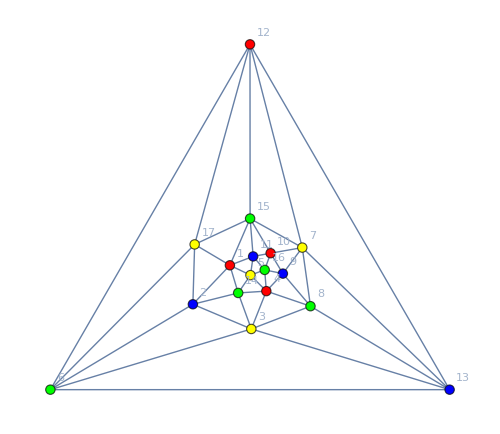
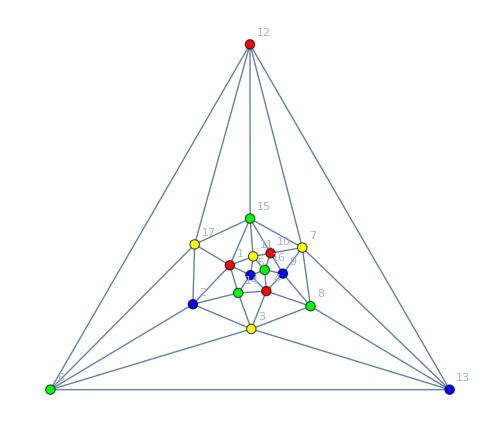
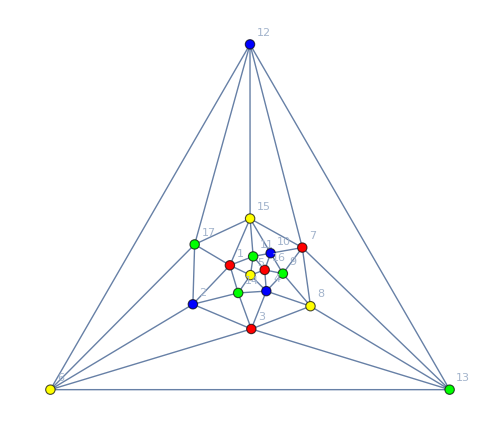
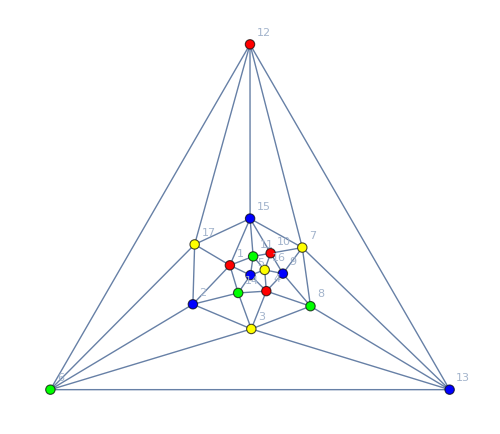
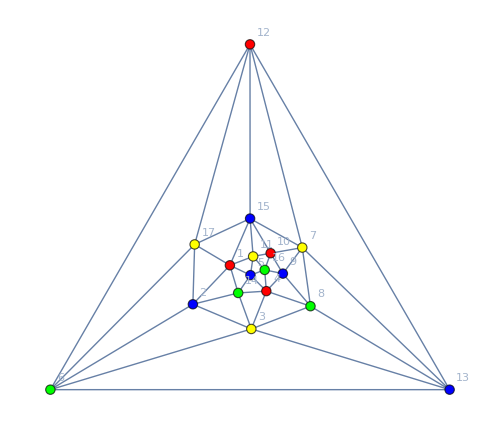
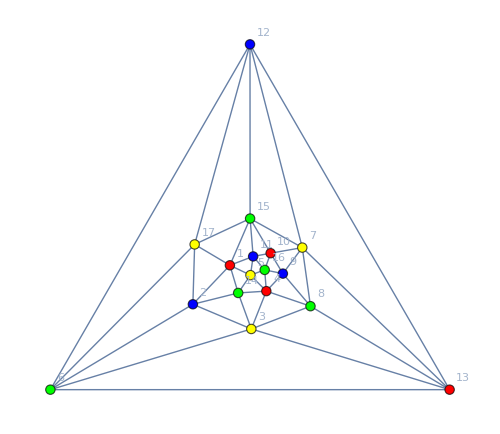
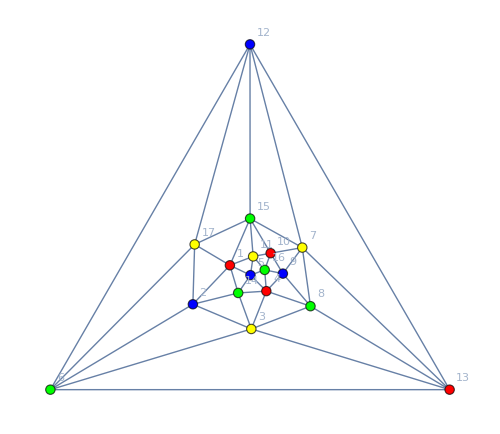
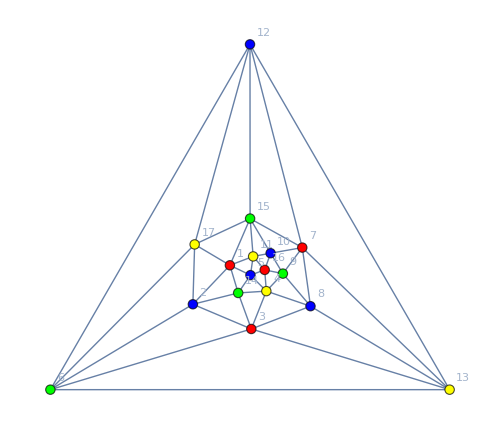

```mathematica
Table[Graph[plantri8,VertexStyle->SymbolToColoring[c],ImageSize->500],{c,FindFullFormula4[plantri8]}]
```

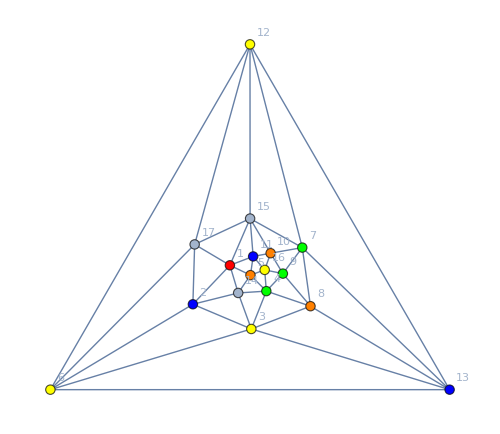
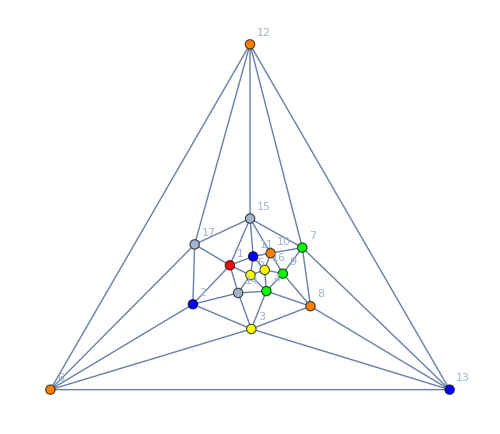
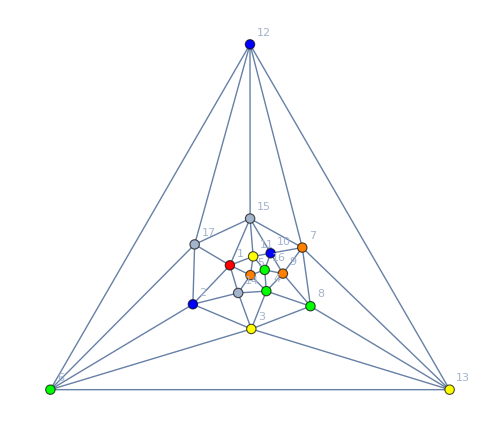
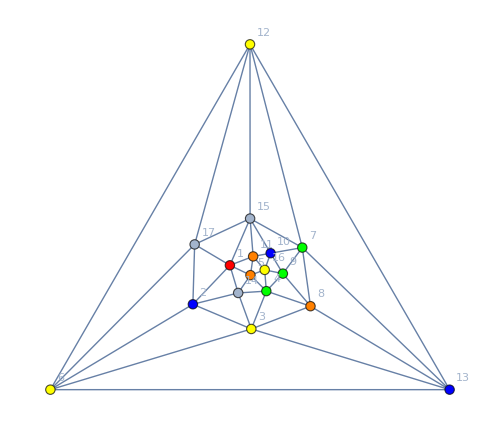

```mathematica
Table[Graph[plantri8,VertexStyle->SymbolToColoring[c],ImageSize->500],{c,Take[Select[femb,SymbolLevel[#]==5&],4]}]
```

```mathematica
Table[PlanarGraphQ[EmbedGraphInPlantri8[allGraphs5,k]]->ShowGraph5Least[k],{k,allGraphs5AtomKeys}]//Sort
```

{False→-Graphics-514780,False→-Graphics-319840,False→-Graphics-368980,False→-Graphics-361940,False→-Graphics-383080,False→-Graphics-514750,False→-Graphics-492100,False→-Graphics-382810,False→-Graphics-319540,False→-Graphics-361660,False→-Graphics-368170,False→-Graphics-297970,False→-Graphics-361120,False→-Graphics-360860,False→-Graphics-303340,False→-Graphics-296330,False→-Graphics-317380,False→-Graphics-295600,False→-Graphics-317140,False→-Graphics-296080,False→-Graphics-492070,False→-Graphics-360850,False→-Graphics-297670,False→-Graphics-317110,False→-Graphics-296050,False→-Graphics-295330,False→-Graphics-302530,False→-Graphics-295510,False→-Graphics-295250,False→-Graphics-295270,False→-Graphics-295240,True→-Graphics-590481,True→-Graphics-582881,True→-Graphics-567701,True→-Graphics-560121,True→-Graphics-522321,True→-Graphics-499721,True→-Graphics-492201,True→-Graphics-390141,True→-Graphics-326841,True→-Graphics-305861,True→-Graphics-298881,True→-Graphics-560111,True→-Graphics-492161,True→-Graphics-499631,True→-Graphics-492081,True→-Graphics-298571,True→-Graphics-304961,True→-Graphics-297681,True→-Graphics-324411,True→-Graphics-302621,True→-Graphics-295371}